```mathematica
T[b_,n_]:=Integrate[n[√(b^2+z^2)],{z,-∞,∞}]
```

## Hard sphere

```mathematica
n1[r_,{A_,R_}]:=3/4 A/(π R^3)HeavisideTheta[R^2-r^2]
```

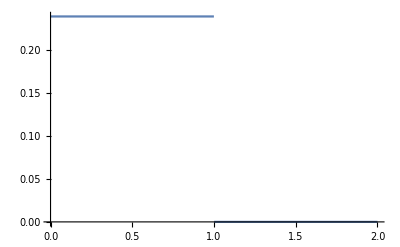

```mathematica
Plot[n1[r,{1,1}],{r,0,2}]
```

```mathematica
T1[b_,{A_,R_}]:=NIntegrate[n1[√(b^2+z^2),{A,R}],{z,-∞,∞}]
```

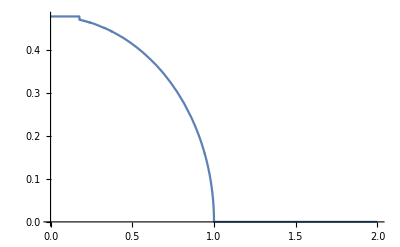

```mathematica
Plot[T1[b,{1,1}],{b,0,2}]
```

## Wood-Saxon

```mathematica
n2[r_,{A_,R_,d_}]:=(3/4 A/(π R^3)1/(1+π^2 d^2/R^2))/(1+Exp[(r-R)/d])
```

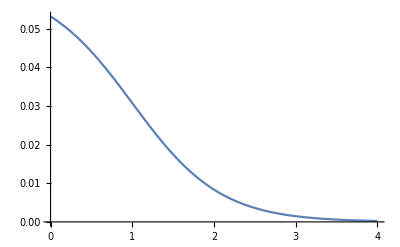

```mathematica
Plot[n2[r,{1,1,0.54}],{r,0,4}]
```

```mathematica
T2[b_,{A_,R_,d_}]:=NIntegrate[n2[√(b^2+z^2),{A,R,d}],{z,-∞,∞}]
```

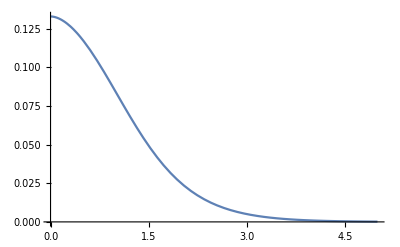

```mathematica
Plot[T2[b,{1,1,0.54}],{b,0,5}]
```

## Effective cross section

```mathematica
σeff[{A_,RA_,dA_},{B_,RB_,dB_},σpp_]=(1/σpp+(2(A-1))/A^2 Integrate[n2[√(b^2+z^2),{A,RA,dA}],{z,-∞,∞},{b,0,∞},Assumptions->{A>0,RA>0,dA>0}]+(2(B-1))/B^2 Integrate[n2[√(b^2+z^2),{B,RB,dB}],{z,-∞,∞},{b,0,∞},Assumptions->{B>0,RB>0,dB>0}])^-1
```

1/(1/σpp-(3 (-1+A) dA^2 PolyLog[2,-ⅇ^(RA/dA)])/(2 A (dA^2 π^2 RA+RA^3))-(3 (-1+B) dB^2 PolyLog[2,-ⅇ^(RB/dB)])/(2 B (dB^2 π^2 RB+RB^3)))

```mathematica
RA[A_]:=1.12 A^(1/3)-0.86 A^(-1/3)
```

```mathematica
plotFunction[A_,σpp_]:=σeff[{1,1,1},{A,RA[A],0.54},σpp]
```

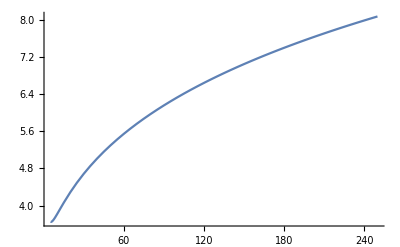

```mathematica
Plot[plotFunction[A,50],{A,5,250}]
```

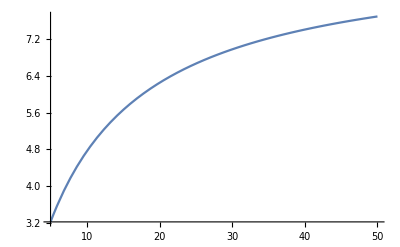

```mathematica
Plot[plotFunction[208,σpp],{σpp,5,50}]
```